Analisi della risposta libera per un sistema TD

```mathematica
A=({{7/15, 4/5, -4/5, 0}, {-13/5, -14/15, 3/5, -2}, {-7/3, -1/3, 0, -2}, {-8/15, -8/15, 8/15, -1/3}})
```

{{7/15,4/5,-4/5,0},{-13/5,-14/15,3/5,-2},{-7/3,-1/3,0,-2},{-8/15,-8/15,8/15,-1/3}}

Calcolo degli autovalori

```mathematica
λ=Eigenvalues[A]
```

{-1/3,-1/3,-1/3,1/5}

Per valutare la diagonalizzabilita’ o meno di A mi calcolo la molteplicita’ geometrica dell’autovalore multiplo 
dim(Ker(A + (1/3) I))

```mathematica
NullSpace[A+1/3 IdentityMatrix[4]]
```

{{-1,1,0,1},{0,1,1,0}}

I modi naturali si “contano” a partire dal polinomio oppure dalla forma di Jordan della matrice A

```mathematica
Factor[ResourceFunction["MatrixMinimalPolynomial"][A,x]]
```

1/45 (1+3 x)^2 (-1+5 x)

Mi calcolo la forma di Jordan di A

```mathematica
Subscript[T, J]=JordanDecomposition[A][[1]]
```

{{-1,0,-1/2,-3/2},{1,1,1/2,3},{0,1,0,5/2},{1,0,0,1}}

```mathematica
Subscript[T, J]//MatrixForm
```

(-1 | 0 | -1/2 | -3/2
1 | 1 | 1/2 | 3
0 | 1 | 0 | 5/2
1 | 0 | 0 | 1)

```mathematica
Subscript[A, J]=JordanDecomposition[A][[2]]
```

{{-1/3,0,0,0},{0,-1/3,1,0},{0,0,-1/3,0},{0,0,0,1/5}}

```mathematica
Subscript[A, J]//MatrixForm
```

(-1/3 | 0 | 0 | 0
0 | -1/3 | 1 | 0
0 | 0 | -1/3 | 0
0 | 0 | 0 | 1/5)

```mathematica
Subscript[T, J]//MatrixForm
```

(-1 | 0 | -1/2 | -3/2
1 | 1 | 1/2 | 3
0 | 1 | 0 | 5/2
1 | 0 | 0 | 1)

Inserisco lo stato iniziale

```mathematica
Subscript[x, 0]={{1},{1},{0},{2}}
```

{{1},{1},{0},{2}}

e lo proietto lungo le componenti della matrice di cambiamento di base

```mathematica
Subscript[z, 0]=Inverse[Subscript[T, J]].Subscript[x, 0]
```

{{4},{5},{-4},{-2}}

Mi scrivo “finalmente” la risposta libera utilizzando la decomposizione di Jordan

```mathematica
Subscript[x, l][k_]:=Subscript[T, J].({{(-1/3)^k, 0, 0, 0}, {0, (-1/3)^k, Binomial[k,1](-1/3)^(k-1), 0}, {0, 0, (-1/3)^k, 0}, {0, 0, 0, (1/5)^k}}).Subscript[z, 0]
```

```mathematica
Subscript[x, l,0][k_]:=MatrixPower[A, k] . x0
```

```mathematica
MatrixForm[Simplify[Subscript[x, l][k]]]
```

(-2 (-1/3)^k+3 5^-k
15^-k (7 (-5)^k-2 3^(1+k)+12 (-5)^k k)
5 (-1/3)^k-5^(1-k)-4 (-1/3)^(-1+k) k
4 (-1/3)^k-2 5^-k)

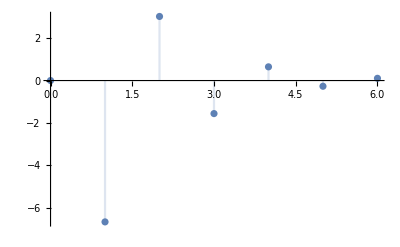

```mathematica
DiscretePlot[Subscript[x, l][k][[3]],{k,0,6},PlotRange->All]
```

Inserisco il vettore di uscita

```mathematica
Cc={-1,2,7,1}
```

{-1,2,7,1}

Mi calcolo la risposta libera nell’uscita

```mathematica
Subscript[y, l][k_]:=Simplify[Cc.Subscript[x, l][k]]
```

```mathematica
Subscript[y, l][k]
```

{55 (-1/3)^k-52 5^-k+4 (-1)^k 3^(3-k) k}

```mathematica
Cc.Subscript[T, J]
```

{4,9,3/2,26}

```mathematica
Subscript[A, J]//MatrixForm
```

(-1/3 | 0 | 0 | 0
0 | -1/3 | 1 | 0
0 | 0 | -1/3 | 0
0 | 0 | 0 | 1/5)

```mathematica
Subscript[T, J]//MatrixForm
```

(-1 | 0 | -1/2 | -3/2
1 | 1 | 1/2 | 3
0 | 1 | 0 | 5/2
1 | 0 | 0 | 1)

```mathematica
MatrixForm[({{(-1/3)^k, 0, 0, 0}, {0, (-1/3)^k, Binomial[k,1](-1/3)^(k-1), 0}, {0, 0, (-1/3)^k, 0}, {0, 0, 0, (1/5)^k}})]
```

((-1/3)^k | 0 | 0 | 0
0 | (-1/3)^k | (-1/3)^(-1+k) k | 0
0 | 0 | (-1/3)^k | 0
0 | 0 | 0 | 5^-k)

```mathematica
Subscript[T, J]//MatrixForm
```

(-1 | 0 | -1/2 | -3/2
1 | 1 | 1/2 | 3
0 | 1 | 0 | 5/2
1 | 0 | 0 | 1)

Ad esempio, se scelgo lo stato iniziale “allineato” secondo la quarta colonna della matrice di cambiamento di base

```mathematica
Subscript[x, 0]={{3},{-6},{-5},{-2}}
```

{{3},{-6},{-5},{-2}}

```mathematica
Subscript[z, 0]=Inverse[Subscript[T, J]].Subscript[x, 0]
```

{{0},{0},{0},{-2}}

```mathematica
Subscript[x, l][k_]:=Subscript[T, J].({{(-1/3)^k, 0, 0, 0}, {0, (-1/3)^k, Binomial[k,1](-1/3)^(k-1), 0}, {0, 0, (-1/3)^k, 0}, {0, 0, 0, (1/5)^k}}).Subscript[z, 0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(3 5^-k
-6 5^-k
-5^(1-k)
-2 5^-k)

Allineo lo stato iniziale secondo la prima colonna della matrice di cambiamento di base, ad es.

```mathematica
Subscript[x, 0]={{5},{-5},{0},{-5}}
```

{{5},{-5},{0},{-5}}

```mathematica
Subscript[z, 0]=Inverse[Subscript[T, J]].Subscript[x, 0]
```

{{-5},{0},{0},{0}}

```mathematica
Subscript[x, l][k_]:=Subscript[T, J].({{(-1/3)^k, 0, 0, 0}, {0, (-1/3)^k, Binomial[k,1](-1/3)^(k-1), 0}, {0, 0, (-1/3)^k, 0}, {0, 0, 0, (1/5)^k}}).Subscript[z, 0]
```

```mathematica
/MatrixForm
```

(5 (-1/3)^k
-5 (-1/3)^k
0
-5 (-1/3)^k)

Se scelgo lo stato iniziale, combinazione lineare della seconda e della terza colonna della matrice di cambiamento di base, associate al miniblocco di Jordan di dimensione due, tutti gli stati successivi resteranno “intrappolati” nel piano di  che si ottiene dalla combinazione lineare della seconda e della terza colonna di , ad es.

```mathematica
Subscript[T, J]//MatrixForm
```

(-1 | 0 | -1/2 | -3/2
1 | 1 | 1/2 | 3
0 | 1 | 0 | 5/2
1 | 0 | 0 | 1)

```mathematica
Subscript[x, 0]={{-1/2},{-1/2},{-1},{0}}
```

{{-1/2},{-1/2},{-1},{0}}

```mathematica
Subscript[x, 0]//MatrixForm
```

(-1/2
-1/2
-1
0)

```mathematica
Subscript[z, 0]=Inverse[Subscript[T, J]].Subscript[x, 0]
```

{{0},{-1},{1},{0}}